# Эффект Джанибекова

## Численное интегрирование уравнений пространственного движения твёрдого тела вокруг неподвижной точки и его визуализация

Самарский университет
Кафедра теоретической механики.
Юдинцев В. В.

## Постановка задачи

Рассмотрим вращение твёрдого тела (гайки-барашка) вокруг центра масс в условиях невесомости. Это движение эквивалентно сферическому движению твердого тела вокруг неподвижной точки, совпадающей с центром масс.

С твёрдым телом связана система координат Cxyz, начало которой совпадает с центром масс тела, а оси направлены так, как показано на рисунке.

Моменты инерции вокруг осей связанной системы координат удовлетворяют следующему условию:

J_x<J_y<J_z

-Graphics-

## Кинематические соотношения

Ориентацию связанной системы координат Cxyz относительно неподвижной системы координат Cx_0 y_0 z_0 будет определяться тремя углами Эйлера последовательности X-Z’-X’’:

Первый поворот совершается вокруг оси x_0 на угол ψ

Второй поворот совершается вокруг новой оси z=z' на угол ϑ

Третий поворот  совершается вокруг новой оси x на угол φ

-Graphics-

Эти три угла позволяют задать угловое положение гайки-барашка в пространстве относительно неподвижной системы координат.

## Матрица преобразования координат

Каждый элементарный поворот можно описать матрицей преобразования координат из новой системы координат (повернутой) в исходную. Например для поворота вокруг оси x на угол ψ матрица преобразования координат (или матрица поворота) имеет вид:

A_x=(1 | 0 | 0
0 | cosψ | −sinψ
0 | sinψ | cosψ)

Предположим, что система координат Cxyz развёрнута относительно неподвижной системы координат Cx_0 y_0 z_0 вокруг оси Cx_0 на угол ψ.

-Graphics-

## Матрица преобразования координат

-Graphics-

Если известны координаты точки (вектора) в повернутой системе, то координаты этой же точки в исходной неподвижной системе координат  будут определяться выражением:

(x
y
z)=(1 | 0 | 0
0 | cosψ | −sinψ
0 | sinψ | cosψ)(x'
y'
z')

Обратное преобразование:

(x'
y'
z')=(1 | 0 | 0
0 | cosψ | −sinψ
0 | sinψ | cosψ)^T(x
y
z)=(1 | 0 | 0
0 | cosψ | sinψ
0 | -sinψ | cosψ)(x
y
z)

## Матрицы элементарных поворотов

Поворот вокруг оси x:

```mathematica
RotationMatrix[ψ,{1,0,0}]
%//MatrixForm
```

{{1,0,0},{0,Cos[ψ],-Sin[ψ]},{0,Sin[ψ],Cos[ψ]}}

(1 | 0 | 0
0 | Cos[ψ] | -Sin[ψ]
0 | Sin[ψ] | Cos[ψ])

Поворот вокруг оси y:

```mathematica
RotationMatrix[ϑ,{0,1,0}];
%//MatrixForm
```

(Cos[ϑ] | 0 | Sin[ϑ]
0 | 1 | 0
-Sin[ϑ] | 0 | Cos[ϑ])

Поворот вокруг оси z:

```mathematica
RotationMatrix[φ,{0,0,1}]
%//MatrixForm
```

{{Cos[φ],-Sin[φ],0},{Sin[φ],Cos[φ],0},{0,0,1}}

(Cos[φ] | -Sin[φ] | 0
Sin[φ] | Cos[φ] | 0
0 | 0 | 1)

## Сложный поворот (последовательность X - Z’ - X”)

-Graphics-

Матрицы элементарных поворотов

```mathematica
A1=RotationMatrix[ψ,{1,0,0}]
```

{{1,0,0},{0,Cos[ψ],-Sin[ψ]},{0,Sin[ψ],Cos[ψ]}}

```mathematica
A2=RotationMatrix[ϑ,{0,0,1}]
```

{{Cos[ϑ],-Sin[ϑ],0},{Sin[ϑ],Cos[ϑ],0},{0,0,1}}

```mathematica
A3=RotationMatrix[φ,{1,0,0}]
```

{{1,0,0},{0,Cos[φ],-Sin[φ]},{0,Sin[φ],Cos[φ]}}

## Сложный поворот

-Graphics-

```mathematica
A1=RotationMatrix[ψ,{1,0,0}]
A2=RotationMatrix[ϑ,{0,0,1}]
A3=RotationMatrix[φ,{1,0,0}]
```

{{1,0,0},{0,Cos[ψ],-Sin[ψ]},{0,Sin[ψ],Cos[ψ]}}

{{Cos[ϑ],-Sin[ϑ],0},{Sin[ϑ],Cos[ϑ],0},{0,0,1}}

{{1,0,0},{0,Cos[φ],-Sin[φ]},{0,Sin[φ],Cos[φ]}}

Матрица сложного поворота определяется произведением  матриц элементарных поворотов в прямом порядке.

Матрица преобразования координат из повернутой системы (после трех поворотов) в исходную:

```mathematica
A123=A1.A2.A3;
A123//MatrixForm
```

(Cos[ϑ] | -Cos[φ] Sin[ϑ] | Sin[ϑ] Sin[φ]
Cos[ψ] Sin[ϑ] | Cos[ϑ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ] | -Cos[ϑ] Cos[ψ] Sin[φ]-Cos[φ] Sin[ψ]
Sin[ϑ] Sin[ψ] | Cos[ψ] Sin[φ]+Cos[ϑ] Cos[φ] Sin[ψ] | Cos[φ] Cos[ψ]-Cos[ϑ] Sin[φ] Sin[ψ])

## Динамические уравнения Эйлера

-Graphics-

Уравнения свободного вращения твердого тела вокруг центра масс в отсутствии внешних моментов (движение “по инерции”):

```mathematica
eq={
Jx wx'[t]==(Jy-Jz) wy[t] wz[t],
Jy wy'[t]==(Jz-Jx) wx[t] wz[t],
Jz wz'[t]==(Jx-Jy) wy[t] wx[t]
};
```

## Динамические уравнения Эйлера

Уравнения свободного вращения твердого тела вокруг центра масс в отсутствии внешних моментов (движение “по инерции”):

```mathematica
eq={
Jx wx'[t]==(Jy-Jz) wy[t] wz[t],
Jy wy'[t]==(Jz-Jx) wx[t] wz[t],
Jz wz'[t]==(Jx-Jy) wy[t] wx[t]
};
```

wx, wy, wz - это проекции угловой скорости тела на связанные оси.

Параметры системы и начальные угловые скорости:

```mathematica
params={Jx->1,Jy->2,Jz->3,wx0->0.001,wy0->1,wz0->0.001};
```

Вращение начинается вокруг оси Cy c угловой скоростью 1 рад/с. 
Также заданы небольшие возмущения угловой скорости вокруг других осей (0,001 рад/с)

-Graphics-

## Численное интегрирование

Подставляем в уравнения движения параметры:

```mathematica
params={Jx->1,Jy->2,Jz->3,wx0->0.001,wy0->1,wz0->0.001};
neq={eq,wx[0]==wx0,wy[0]==wy0,wz[0]==wz0}//.params//Flatten
```

{wx'[t]==-wy[t] wz[t],2 wy'[t]==2 wx[t] wz[t],3 wz'[t]==-wx[t] wy[t],wx[0]==0.001,wy[0]==1,wz[0]==0.001}

```mathematica
tk=60;
sol=NDSolve[neq,{wx[t],wy[t],wz[t]},{t,0,tk}]//Flatten;
```

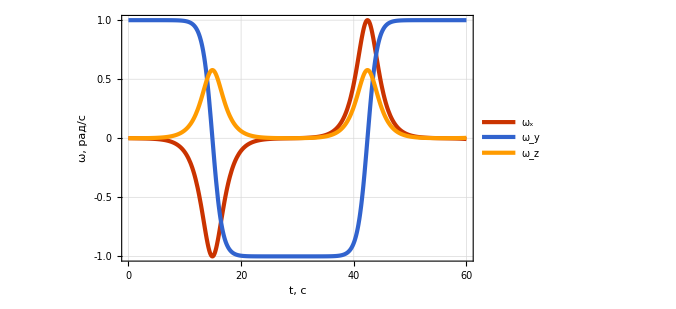

```mathematica
Plot[{wx[t],wy[t],wz[t]}//.sol//Evaluate,{t,0,tk},ImageSize->500,FrameLabel->{"t, c","ω, рад/с"},PlotLegends->Placed[{"ω_x","ω_y","ω_z"},{Right,Bottom}],PlotTheme->{"Web","FrameGrid"}]
```

В результате интегрирования динамических уравнений Эйлера получаются проекции угловые скорости.

Как определить углы ориентации связанной системы координат относительно неподвижной?

## Кинематические уравнения

Кинематические уравнения связывают проекции угловой скорости с производными углов.

-Graphics-

Выразим проекции угловой скорости на связанные оси тела через производные углов

ω_x=φ̇+ψ̇·cos ϑ 
ω_y=ϑ̇ sin φ -ψ̇ sin ϑ cos φ  
ω_z=ϑ̇ cos φ +ψ̇ sin ϑ sin φ

Выражение производных углов через угловые скорости (кинематические уравнения):

ψ̇ | =(ω_z sinφ−ω_y cosφ)/sinϑ 
ϑ̇ = ω_z cos φ+ω_y sinφ;    
φ̇=ω_x+(ω_y cosφ−ω_z sinφ)/tanϑ

## Кинематические уравнения

```mathematica
kinematicEq={
ψ'[t]==(wz[t] Sin[φ[t]]-wy[t] Cos[φ[t]])/Sin[ϑ[t]],
ϑ'[t]==wz[t] Cos[φ[t]]+wy[t] Sin[φ[t]],
φ'[t]==wx[t]+(wy[t] Cos[φ[t]]-wz[t] Sin[φ[t]])/Tan[ϑ[t]]
};
```

```mathematica
params={Jx->1,Jy->2,Jz->3,wx0->0.001,wy0->1,wz0->0.001,ψ0->0.0,ϑ0->π/2,φ0->0.0};
```

Уравнения движения: динамические + кинематические

```mathematica
neq={
eq,kinematicEq,
wx[0]==wx0,wy[0]==wy0,wz[0]==wz0,
ψ[0]==ψ0,ϑ[0]==ϑ0,φ[0]==φ0
}//.params//Flatten
```

{wx'[t]==-wy[t] wz[t],2 wy'[t]==2 wx[t] wz[t],3 wz'[t]==-wx[t] wy[t],ψ'[t]==Csc[ϑ[t]] (-Cos[φ[t]] wy[t]+Sin[φ[t]] wz[t]),ϑ'[t]==Sin[φ[t]] wy[t]+Cos[φ[t]] wz[t],φ'[t]==wx[t]+Cot[ϑ[t]] (Cos[φ[t]] wy[t]-Sin[φ[t]] wz[t]),wx[0]==0.001,wy[0]==1,wz[0]==0.001,ψ[0]==0.,ϑ[0]==π/2,φ[0]==0.}

## Результат

```mathematica
neq={{eq,kinematicEq},wx[0]==wx0,wy[0]==wy0,wz[0]==wz0,ψ[0]==ψ0,ϑ[0]==ϑ0,φ[0]==φ0}//.params//Flatten
```

{wx'[t]==-wy[t] wz[t],2 wy'[t]==2 wx[t] wz[t],3 wz'[t]==-wx[t] wy[t],ψ'[t]==Csc[ϑ[t]] (-Cos[φ[t]] wy[t]+Sin[φ[t]] wz[t]),ϑ'[t]==Sin[φ[t]] wy[t]+Cos[φ[t]] wz[t],φ'[t]==wx[t]+Cot[ϑ[t]] (Cos[φ[t]] wy[t]-Sin[φ[t]] wz[t]),wx[0]==0.001,wy[0]==1,wz[0]==0.001,ψ[0]==0.,ϑ[0]==π/2,φ[0]==0.}

```mathematica
tk=60;
sol=NDSolve[neq,{wx[t],wy[t],wz[t],ψ[t],ϑ[t],φ[t]},{t,0,tk}]//Flatten;
```

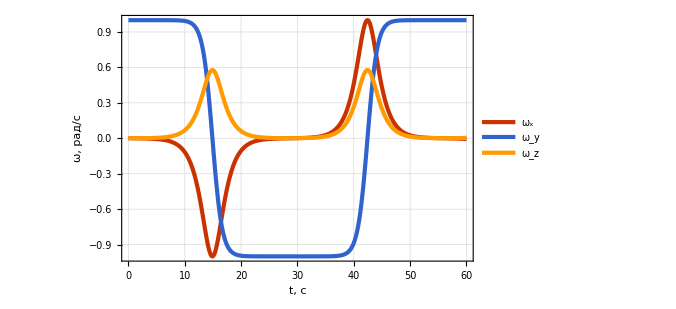

```mathematica
Plot[{wx[t],wy[t],wz[t]}//.sol//Evaluate,{t,0,tk},ImageSize->500,FrameLabel->{"t, c","ω, рад/с"},PlotLegends->{"ω_x","ω_y","ω_z"},PlotTheme->{"Web","FrameGrid"}]
```

## Углы

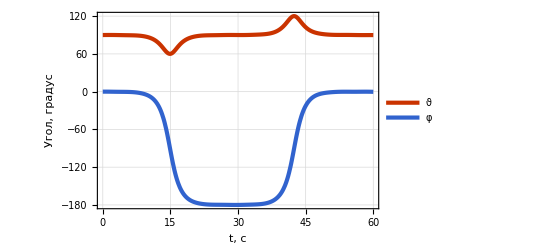

```mathematica
Plot[{ϑ[t],φ[t]}*180/π//.sol//Evaluate,{t,0,tk},ImageSize->400,FrameLabel->{"t, c","Угол, градус"},PlotLegends->{"ϑ","φ"},PlotTheme->{"Web","FrameGrid"}]
```

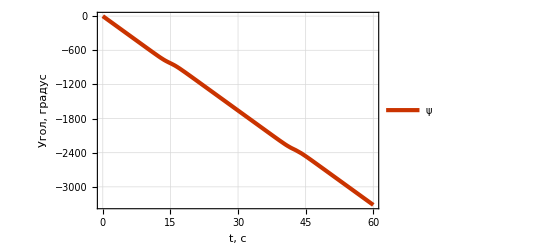

```mathematica
Plot[ψ[t]*180/π//.sol//Evaluate,{t,0,tk},ImageSize->400,FrameLabel->{"t, c","Угол, градус"},PlotLegends->{"ψ"},PlotTheme->{"Web","FrameGrid"}]
```

## Импорт 3D модели объекта

```mathematica
object=Import[NotebookDirectory[]<>"screw.stl",{"GraphicsComplex"}];
```

```mathematica
Graphics3D[{object},Axes->True]
```

-Graphics3D-

```mathematica
Graphics3D[{EdgeForm[None],object},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Поворот объекта в пространстве

Поворот объекта вокруг оси y

```mathematica
Graphics3D[
{
EdgeForm[None],
GeometricTransformation[object,RotationMatrix[30°,{0,1,0}]]
},
Axes->True,AxesLabel->{"x","y","z"}
]
```

-Graphics3D-

## Поворот объекта в пространстве

Матрица сложного поворота

```mathematica
A123=.;
A123[ψ_,ϑ_,φ_]:=RotationMatrix[ψ,{1,0,0}].RotationMatrix[ϑ,{0,0,1}].RotationMatrix[φ,{1,0,0}];
```

```mathematica
Manipulate[
Graphics3D[
{
{Green,Arrow[{{0,0,0},{0,1,0}}]},
{Red,Arrow[{{0,0,0},{1,0,0}}]},
EdgeForm[None],
GeometricTransformation[{object,Arrow[{{0,0,0},{0,1,0}}]},A123[ψ,ϑ,φ]]
},
Axes->False,AxesLabel->{"x","y","z"},PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False
],
{ψ,0,2π},{ϑ,0,2π},{φ,0,2 π}]
```

## Анимация

```mathematica
Animate[
Graphics3D[
{
EdgeForm[None],
GeometricTransformation[object,{A123[ψ[t],ϑ[t],φ[t]]/.sol,{0,0,0}}]
},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-1,1},{-1,1},{-1,1}}
]/.t->tt,
{tt,0,tk,0.2},DisplayAllSteps->True]
```

## Экспорт анимации в файл (gif)

#### Анимированный GIF

Формируем список отдельных кадров

```mathematica
aniTable = Table[
   Graphics3D[
     {
      EdgeForm[None],
      GeometricTransformation[object, {A123[ψ[t], ϑ[t], φ[t]] /. sol, {0, 0, 0}}]
      },
     Axes -> True, AxesLabel -> {"x", "y", "z"}, PlotRange -> {{-1, 1}, {-1, 1}, {-1, 1}}
     ] /. t -> tt,
   {tt, 0, tk, 0.5}];
```

Экспортируем в файл

```mathematica
Export[NotebookDirectory[]<>"res.gif",aniTable];
```

Можно и в avi (файл большого размера)

```mathematica
(*
Export[NotebookDirectory[]<>"res.avi",aniTable];
*)
```